```mathematica
(*Experimental Parameters *) 


sq0=12;
asq0=12;
μA0=0.03;
μB0=0.06;
G0=GAB[sq0,asq0,μA0,μB0,0,0];
CM[μB_]:=GAB[sq0,asq0,μA0,μB,0,0];
a0=1.001;
ϵA0=10^-7;
α0= 51.2;
alphabet0=α0/0.1//N;
```

```mathematica
BmajTable=Table[{delta,BMa[a0,delta]},{delta,0.05,3,0.1}]
BmajFu=Interpolation[BmajTable];
xiOTmin[n_,epsA_]:=Minimize[{xiOT[a0,n,epsA,ϵ,epsα[G0,α0,n]],epsα[G0,α0,n]<ϵ<epsA/5 },ϵ][[1]]
rMajOT1[d_,n_,epsA_]:=BmajFu[d]-xiOTmin[n,epsA]
```

{{0.05,3.72461},{0.15,2.93936},{0.25,2.55964},{0.35,2.30412},{0.45,2.10937},{0.55,1.95117},{0.65,1.81696},{0.75,1.70016},{0.85,1.59699},{0.95,1.50361},{1.05,1.41848},{1.15,1.33951},{1.25,1.26651},{1.35,1.19826},{1.45,1.13406},{1.55,1.07487},{1.65,1.01783},{1.75,0.963611},{1.85,0.911951},{1.95,0.862664},{2.05,0.8156},{2.15,0.770614},{2.25,0.727537},{2.35,0.686172},{2.45,0.646308},{2.55,0.607739},{2.65,0.570294},{2.75,0.533848},{2.85,0.498339},{2.95,0.46376}}

```mathematica
ECTable1=Table[{delta,EC[delta,G0,0.98]},{delta,0.05,3,0.1}]
ECFu1=Interpolation[ECTable1];
rMajOT[d_,n_,epsA_]:=1/2(rMajOT1[d,n,epsA]-ECFu1[d])
```

{{0.05,5.30325},{0.15,3.71828},{0.25,2.98132},{0.35,2.49589},{0.45,2.23748},{0.55,1.99417},{0.65,1.80481},{0.75,1.65406},{0.85,1.5319},{0.95,1.43122},{1.05,1.34674},{1.15,1.27451},{1.25,1.21162},{1.35,1.15594},{1.45,1.10596},{1.55,1.06062},{1.65,1.01914},{1.75,0.980969},{1.85,0.945663},{1.95,0.912887},{2.05,0.882353},{2.15,0.853852},{2.25,0.827163},{2.35,0.802115},{2.45,0.778557},{2.55,0.756354},{2.65,0.73539},{2.75,0.715558},{2.85,0.696766},{2.95,0.67893}}

```mathematica
lOTMaj[d_,n_,epsA_,ν_,Nmax_,eta_,Nmean_,Vnoise_]:= n/2*(rMajOT[d,n,epsA]- ν*CapCltherm[eta,Nmean,Vnoise,Nmax]) - Log[2,1/(epsA-4*(epsA/5))] 
lOTMaj[d_,n_,epsA_,ν_,Nmax_,eta_]:= lOTMaj[d,n,epsA,ν,Nmax,eta,0,0]
rateOTMaj[d_,n_,epsA_,ν_,Nmax_,eta_,Nmean_,Vnoise_]:= 1/2*(rMajOT[d,n,epsA]- ν*CapCltherm[eta,Nmean,Vnoise,Nmax]) - 1/n Log[2,1/(epsA-4*(epsA/5))] 
rateOTMaj[d_,n_,epsA_,ν_,Nmax_,eta_]:= rateOTMaj[d,n,epsA,ν,Nmax,eta,0,0]
```

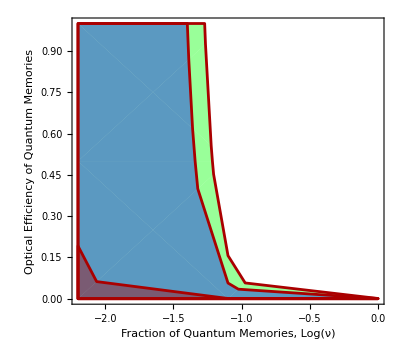

```mathematica
SecureOT=RegionPlot[{rateOTgauss[0.1001,G0,0.944,1.99*10^5,ϵA0,α0,10^k,100,η]>=0,rateOTiid[0.1,10^8,G0,0.944,10,ϵA0,α0,10^k,100,η]>=0,rateOTMaj[1.0,10^8,ϵA0,10^k,100,η]>=0},{k,-2.2,0},{η,0,1},LabelStyle->Directive[Black,FontSize->12],AspectRatio->0.9,PlotPoints->2,BoundaryStyle-> {{Thickness[0.005],Green},{Thickness[0.005],Blue} ,{Thickness[0.005],Darker[Red]}},PlotStyle->{Directive[Green,Opacity[0.4]],Directive[Blue,Opacity[0.4]] ,Directive[Darker[Red],Opacity[0.4]]},
FrameStyle->Thickness[0.0035],Frame->{{True,True},{True,True}},FrameLabel-> {"Fraction of Quantum Memories, Log(ν)","Optical Efficiency of Quantum Memories"}]
```

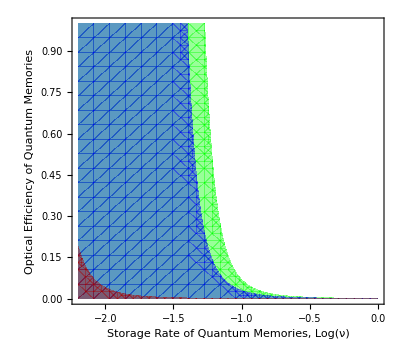

```mathematica
RegionPlot[{rateOTgauss[0.1001,G0,0.944,1.99*10^5,ϵA0,α0,10^k,100,η]≥0,rateOTiid[0.1,10^8,G0,0.944,10,ϵA0,α0,10^k,100,η]≥0,rateOTMaj[1.0,10^8,ϵA0,10^k,100,η]≥0},{k,-2.2,0},{η,0,1},LabelStyle->Directive[Black,FontSize->12],AspectRatio->0.9,BoundaryStyle->None,PlotStyle->{Directive[Green,Opacity[0.4]],Directive[Blue,Opacity[0.4]],Directive[Darker[Red],Opacity[0.4]]},FrameStyle->Thickness[0.0035],Frame->{{True,True},{True,True}},FrameLabel->{"Storage Rate of Quantum Memories, Log(ν)","Optical Efficiency of Quantum Memories"}]
```

```mathematica
Export["SecureOT12dB.pdf",SecureOT]
```

SecureOT12dB.pdf

```mathematica
{Directive[Thickness[0.005],Green],Directive[Thickness[0.005],Blue],Directive[Thickness[0.005],Darker[Red]]}
```

{Directive[Thickness[0.005],RGBColor[0, 1, 0]],Directive[Thickness[0.005],RGBColor[0, 0, 1]],Directive[Thickness[0.005],RGBColor[Rational[2, 3], 0, 0]]}

```mathematica
Export["SecureOT.pdf",SecureOT]
```

RegionPlot::ppts: Value of option PlotPoints -> 1 is not an integer >= 2.

SecureOT.pdf